```mathematica
(*Configuration*)
a=1;
b=-0.1+ⅈ*0.001;
k=100;
t=0.1;
A=1;
X0=2;

Epsilon = Function[x,Piecewise[{{1,Re[a*x^2+b]>1}},a*x^2+b]];
```

{0.695142}

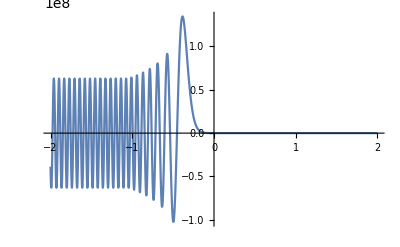

```mathematica
(*TE-wave*)
ETEEquation={y''[x]+k^2*(Epsilon[x]-Sin[t]^2)*y[x]==0};
ETEInitials={y[X0]==A,y'[X0]==ⅈ*k*A};

ETE=NDSolveValue[{ETEEquation,ETEInitials},y,{x,-X0,X0}];

RTSystem={
ETE[-X0]==Amp*(Exp[ⅈ*k*(-X0)]+R*Exp[-ⅈ*k*(-X0)]),
ETE'[-X0]==ⅈ*k*Amp*(Exp[ⅈ*k*(-X0)]-R*Exp[-ⅈ*k*(-X0)]),
ETE[X0]==Amp*T*Exp[ⅈ*k*(X0)]};
RTSolution=NSolve[RTSystem,{R,T,Amp}];
Abs[R/.RTSolution]^2+Abs[T/.RTSolution]^2


BTE=Function[x,(-ⅈ/k)*ETE'[x]*Cos[t]];

STE[x_]={ETE[x]*Conjugate[BTE[x]],0,-ETE[x]*Conjugate[-Sin[t]*ETE[x]]};
DeltaEnergy=Function[x,(Norm[Re[STE[x]]]-Norm[Re[STE[-X0]]])/Norm[Re[STE[-X0]]]];
Plot[DeltaEnergy[x],{x,-X0,X0},PlotRange->{{-X0,X0}},PlotStyle->{Bold,Red}];
Plot[Re[ETE[x]],{x,-X0,X0}]
```

{0.403673}

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

General::stop: Further output of Norm :: nvm will be suppressed during this calculation.

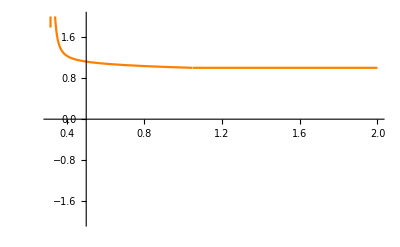

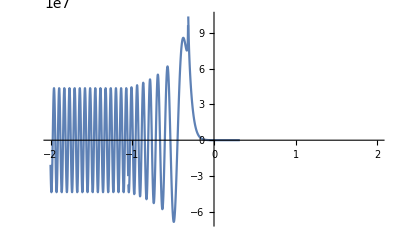

```mathematica
(*TM-wave*)
step=0.0000000001;
Singularity =DSolveValue[D[y[x,x0],{x,2}]-(2a*x0/(2a*x0+ⅈ*Im[Epsilon[x0]]))*D[y[x,x0],x]-k^2*Sin[t]^2*y[x,x0]==0,y,{x,x0}];
x1=Sqrt[-Re[b]/a];
x2=-x1;

BTMEquation={y''[x]-(Epsilon'[x]/Epsilon[x])*y'[x]+k^2*(Epsilon[x]-Sin[t]^2)*y[x]==0};

(*Right and simpliest part*)
BTMInitials1={y[X0]==-A,y'[X0]==-ⅈ*k*Epsilon[X0]*A*Cos[t]};
BTM1=NDSolveValue[{BTMEquation,BTMInitials1},y,{x,x1+step,X0}];

firstPoint=
{Singularity[x1+step,x1]==BTM1[x1+step],
(D[Singularity[x,y],x]/.{x->x1+step,y->x1})==BTM1'[x1+step]};
firstSol=NSolve[firstPoint,{C[1][x1],C[2][x1]}];

(*Middle part*)
BTMInitials2={y[x1-step]==(Singularity[x1-step,x1]/.firstSol),y'[x1-step]==(D[Singularity[x,y],x]/.{x->x1-step,y->x1}/.firstSol)};
BTM2=NDSolveValue[{BTMEquation,BTMInitials2},y,{x,x2+step,x1-step}];

secondPoint=
{Singularity[x2+step,x2]==BTM2[x2+step],
(D[Singularity[x,y],x]/.{x->x2+step,y->x2})==BTM2'[x2+step]};
secondSol=NSolve[secondPoint,{C[1][x2],C[2][x2]}];

(*Last and most important part*)
BTMInitials3={y[x2-step]==(Singularity[x2-step,x2]/.secondSol),y'[x2-step]==(D[Singularity[x,y],x]/.{x->x2-step,y->x2}/.secondSol)};
BTM3=NDSolveValue[{BTMEquation,BTMInitials3},y,{x,-X0,x2-step}];

BTM=Function[x,Piecewise[{{BTM1[x],x>x1+step},{BTM2[x],x1-step>x>x2+step},{BTM3[x],x<x2-step}}]];

RTSystem={
BTM[-X0]==Amp*(Exp[ⅈ*k*(-X0)]+R*Exp[-ⅈ*k*(-X0)]),
BTM'[-X0]==ⅈ*k*Amp*(Exp[ⅈ*k*(-X0)]-R*Exp[-ⅈ*k*(-X0)]),
BTM[X0]==Amp*T*Exp[ⅈ*k*(X0)]};
RTSolution=NSolve[RTSystem,{R,T,Amp}];
Abs[R/.RTSolution]^2+Abs[T/.RTSolution]^2


ETM=Function[x,Piecewise[{{ⅈ*BTM1'[x]/(k*Epsilon[x]),x>x1+step},{ⅈ*BTM2'[x]/(k*Epsilon[x]),x1-step>x>x2+step},{ⅈ*BTM3'[x]/(k*Epsilon[x]),x<x2-step}}]];

STM[x_]={-ETM[x]*Conjugate[BTM[x]],0,Sin[t]*BTM[x]*Conjugate[BTM[x]]/Epsilon[x]};
Plot[Norm[Re[STM[x]]],{x,-X0,X0},PlotRange->{{-X0,X0}},PlotStyle->{Orange}]
Plot[Re[ETM[x]],{x,-X0,X0}]
```